```mathematica
points={RandomReal[1],RandomReal[1]}&/@Range[100];
```

```mathematica
edgeList={};
```

```mathematica
Module[{point=#},(If[((Abs[#[[2]]-point[[2]]])^2>((Abs[#[[1]]-point[[1]]])^2))&&Last[point]>Last[#],edgeList=Append[edgeList,DirectedEdge[point,#]]])&/@points]&/@points;
```

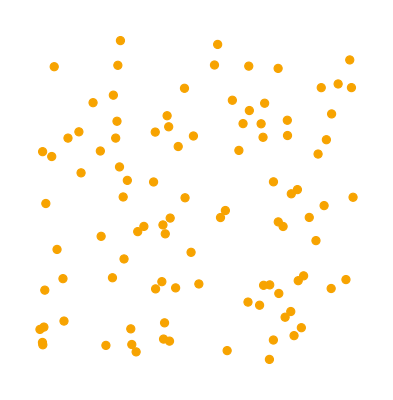

```mathematica
GraphPlot[Graph[points,{},VertexStyle->Directive[Hue[0.11, 1, 0.97],EdgeForm[{Hue[0.11, 1, 0.97],Opacity[1]}]],EdgeStyle->Hue[0, 1, 0.56],VertexCoordinates->((#->#)&/@VertexList[Graph[edgeList]])]]
```

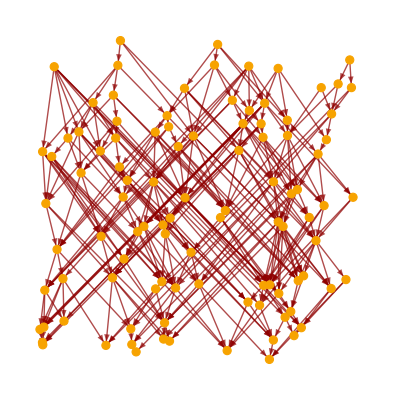

```mathematica
graph=TransitiveReductionGraph[Graph[edgeList],
VertexCoordinates->((#->#)&/@VertexList[Graph[edgeList]]),VertexStyle->Directive[Hue[0.11, 1, 0.97],EdgeForm[{Hue[0.11, 1, 0.97],Opacity[1]}]],EdgeStyle->Hue[0, 1, 0.56]]
```

```mathematica
GraphPlot[graph,VertexLabels->Placed[Automatic,Tooltip]]
```

-Graphics-

```mathematica
VertexList[graph]
```

{{0.399045,0.424351},{0.419567,0.0620974},{0.511249,0.240327},{0.241283,0.259689},{0.301682,0.0515585},{0.731754,0.00509164},{0.599661,0.0325264},{0.315216,0.0285788},{0.220807,0.0487515},{0.400922,0.0684619},{0.744151,0.0655404},{0.404074,0.119088},{0.406322,0.39658},{0.438605,0.228066},{0.395608,0.247471},{0.29852,0.100325},{0.376023,0.224946},{0.339462,0.419709},{0.0236237,0.0506495},{0.277439,0.318287},{0.027011,0.105832},{0.0225075,0.0579866},{0.0898026,0.12464},{0.466335,0.850352},{0.0297776,0.221042},{0.468123,0.509008},{0.374991,0.713832},{0.664791,0.183826},{0.732708,0.237408},{0.701025,0.174015},{0.877211,0.375451},{0.494289,0.701638},{0.0680617,0.34795},{0.59412,0.469256},{0.287755,0.563266},{0.970932,0.253974},{0.744401,0.558742},{0.578906,0.447359},{0.821806,0.250561},{0.838577,0.265608},{0.412055,0.76482},{0.636351,0.65667},{0.369766,0.558276},{0.263265,0.605218},{0.205865,0.388818},{0.798465,0.154372},{0.446754,0.668849},{0.761114,0.210678},{0.320172,0.403466},{0.274771,0.511536},{0.808726,0.0792063},{0.924727,0.226164},{0.774495,0.419543},{0.713524,0.236081},{0.0146699,0.0986121},{0.856253,0.447727},{0.831538,0.103956},{0.486917,0.338951},{0.780768,0.136653},{0.759416,0.433809},{0.086596,0.256874},{0.421657,0.445717},{0.416979,0.73036},{0.909783,0.690022},{0.819264,0.534451},{0.800147,0.521427},{0.902629,0.484624},{0.883815,0.645371},{0.993123,0.510576},{0.255428,0.747611},{0.25132,0.695093},{0.03305,0.491144},{0.14316,0.586722},{0.203437,0.654827},{0.13638,0.714626},{0.982799,0.938785},{0.926083,0.77044},{0.988073,0.852454},{0.788305,0.703124},{0.946502,0.863868},{0.669042,0.781001},{0.70582,0.73968},{0.711831,0.697589},{0.649349,0.74024},{0.787707,0.750687},{0.615956,0.813065},{0.667212,0.919459},{0.716818,0.803782},{0.051484,0.637625},{0.56009,0.922949},{0.244071,0.828914},{0.266206,0.999047},{0.102265,0.695057},{0.180643,0.805502},{0.0229836,0.652761},{0.258118,0.922011},{0.570008,0.987083},{0.89373,0.852346},{0.758959,0.91236},{0.0592656,0.917652}}

```mathematica
inComponent=VertexInComponent[graph,{0.48691704414363257,0.3389512884035131}]
```

{{0.486917,0.338951},{0.287755,0.563266},{0.578906,0.447359},{0.421657,0.445717},{0.13638,0.714626},{0.988073,0.852454},{0.374991,0.713832},{0.263265,0.605218},{0.416979,0.73036},{0.203437,0.654827},{0.59412,0.469256},{0.468123,0.509008},{0.369766,0.558276},{0.70582,0.73968},{0.244071,0.828914},{0.180643,0.805502},{0.0592656,0.917652},{0.982799,0.938785},{0.412055,0.76482},{0.25132,0.695093},{0.255428,0.747611},{0.494289,0.701638},{0.636351,0.65667},{0.446754,0.668849},{0.788305,0.703124},{0.711831,0.697589},{0.649349,0.74024},{0.716818,0.803782},{0.615956,0.813065},{0.669042,0.781001},{0.258118,0.922011},{0.466335,0.850352},{0.56009,0.922949},{0.667212,0.919459},{0.266206,0.999047},{0.946502,0.863868},{0.787707,0.750687},{0.89373,0.852346},{0.570008,0.987083},{0.758959,0.91236}}

```mathematica
L0=DeleteDuplicates[First/@Select[Catenate[FindPath[graph,#,{0.48691704414363257,0.3389512884035131},Infinity,All]&/@inComponent],Length[#]==2&]]
```

{{0.287755,0.563266},{0.578906,0.447359},{0.421657,0.445717},{0.13638,0.714626},{0.988073,0.852454}}

```mathematica
L1=DeleteDuplicates[First/@Select[Catenate[FindPath[graph,#,{0.48691704414363257,0.3389512884035131},Infinity,All]&/@inComponent],Length[#]==3&]]
```

{{0.374991,0.713832},{0.263265,0.605218},{0.416979,0.73036},{0.203437,0.654827},{0.59412,0.469256},{0.468123,0.509008},{0.369766,0.558276},{0.70582,0.73968},{0.244071,0.828914},{0.180643,0.805502},{0.0592656,0.917652},{0.982799,0.938785}}

```mathematica
L2=DeleteDuplicates[First/@Select[Catenate[FindPath[graph,#,{0.48691704414363257,0.3389512884035131},Infinity,All]&/@inComponent],Length[#]==4&]]
```

{{0.374991,0.713832},{0.244071,0.828914},{0.180643,0.805502},{0.0592656,0.917652},{0.412055,0.76482},{0.25132,0.695093},{0.255428,0.747611},{0.494289,0.701638},{0.636351,0.65667},{0.446754,0.668849},{0.788305,0.703124},{0.711831,0.697589},{0.649349,0.74024},{0.716818,0.803782},{0.615956,0.813065},{0.669042,0.781001},{0.258118,0.922011}}

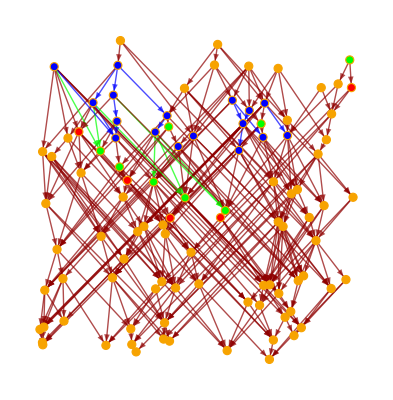

```mathematica
HighlightGraph[graph,{Style[Subgraph[graph,L0],Red],Style[Subgraph[graph,L1],Green],Style[Subgraph[graph,L2],Blue]}]
```